# Equations of motion

We follow the computation for the Kerr BH, note that we may obtain the Schwarzschild case by immediately setting a=0 in any of our equations.

## Lagrangian and Eqns of motion (for an equatorial orbit)

Starting with the Kerr metric, we find 4 equations of motion for our 4 coordinates

```mathematica
η[r,θ] = r^2+a^2 Cos[θ]^2;
Δ[r] = r^2-2M r+a^2;
g1={{-(1-2(M r)/η[r,θ]),0,0,-2a M r Sin[θ]^2/η[r,θ]},{0,η[r,θ]/Δ[r],0,0},{0,0,η[r,θ],0},{-2a M r Sin[θ]^2/η[r,θ],0,0, (Δ[r]+2M r(r^2+a^2)/η[r,θ])Sin[θ]^2}};
g=g1/.t->t[s]/.r->r[s]/.θ->θ[s]/.ϕ->ϕ[s];
ut = t'[s];
ur = r'[s];
uθ = θ'[s] ;
uϕ = ϕ'[s];
utotal = {ut, ur, uθ, uϕ};
L=1/2 g.utotal.utotal;
D[L,ut]==-e/.θ[s]->π/2//Simplify
D[D[L,ur],s]-D[L,r[s]]==0/.θ[s]->π/2//Simplify
D[D[L,uθ],s]-D[L,θ[s]]==0/.θ[s]->π/2//Simplify
D[L,uϕ]==l/.θ[s]->π/2//Simplify
```

e+(-1+(2 M)/r[s]) t'[s]==(2 a M ϕ'[s])/r[s]

(M (t'[s]-a ϕ'[s])^2)/r[s]^2+r[s] (r'[s]^2/(a^2-2 M r[s]+r[s]^2)-θ'[s]^2-ϕ'[s]^2)+(r[s]^2 (M r'[s]^2+(a^2-2 M r[s]+r[s]^2) r''[s]))/((a^2-2 M r[s]+r[s]^2)^2)==(r[s]^3 r'[s]^2)/((a^2-2 M r[s]+r[s]^2)^2)

r[s] (2 r'[s] θ'[s]+r[s] θ''[s])==0

(-2 a M t'[s]+(2 a^2 M+a^2 r[s]+r[s]^3) ϕ'[s])/r[s]==l

## Values for t’(s) , ϕ’(s) and r(s)

Simultaneous equations from t and ϕ eqns of motion, for unknowns t’(s) and ϕ’(s)
Circular orbit (θ = constant, r = constant) turns r eqn of motion into an equation of r in terms of M, a and l (ie. constant)

```mathematica
Solve[e+(-1+(2 M)/r[s]) t'[s]==(2 a M ϕ'[s])/r[s]/.ϕ'[s]->(2 a e M-2 l M+l r[s])/(r[s] (a^2-2 M r[s]+r[s]^2)), t'[s]]
Solve[(-2 a M t'[s]+(2 a^2 M+a^2 r[s]+r[s]^3) ϕ'[s])/r[s]==l/.t'[s]->(-e r[s]+2 a M ϕ'[s])/(2 M-r[s]), ϕ'[s]]
Solve[(M (t'[s]-a ϕ'[s])^2)/r[s]^2+r[s] (r'[s]^2/(a^2-2 M r[s]+r[s]^2)-θ'[s]^2-ϕ'[s]^2)+(r[s]^2 (M r'[s]^2+(a^2-2 M r[s]+r[s]^2) r''[s]))/((a^2-2 M r[s]+r[s]^2)^2)==(r[s]^3 r'[s]^2)/((a^2-2 M r[s]+r[s]^2)^2)/.θ'[s]->0/.r'[s]->0/.r''[s]->0,r[s]]
```

{{t'[s]→(2 a^2 e M-2 a l M+a^2 e r[s]+e r[s]^3)/(r[s] (a^2-2 M r[s]+r[s]^2))}}

{{ϕ'[s]→(2 a e M-2 l M+l r[s])/(r[s] (a^2-2 M r[s]+r[s]^2))}}

{{r[s]→(M^(1/3) (t'[s]-a ϕ'[s])^(2/3))/ϕ'[s]^(2/3)},{r[s]→-((-1)^(1/3) M^(1/3) (t'[s]-a ϕ'[s])^(2/3))/ϕ'[s]^(2/3)},{r[s]→((-1)^(2/3) M^(1/3) (t'[s]-a ϕ'[s])^(2/3))/ϕ'[s]^(2/3)}}

Which can be written as r = (M^(1/3)(1/Ω-a))^(2/3)

## Values for e and l (Chandrasekhar method)

Timelike geodesics so 2L = -1, solve for (r(s))^2 r'(s)^2,  use substitution u=1/r and we obtain an equation for u^-4(u')^2;

```mathematica
Solve[2L==-1/.t'[s]->(2 a^2 e M-2 a l M+a^2 e r[s]+e r[s]^3)/(r[s] (a^2-2 M r[s]+r[s]^2))/.ϕ'[s]->(2 a e M-2 l M+l r[s])/(r[s] (a^2-2 M r[s]+r[s]^2))/.θ[s]->π/2/.θ'[s]->0,r'[s]];
Simplify[r^2((√(a^2-2 M r+r^2) √((2 (-a e+l)^2 M+(a^2 (-1+e^2)-l^2) r+2 M r^2+(-1+e^2) r^3)/(r (a^2-2 M r+r^2))))/r)^2];
```

```mathematica
Simplify[%/r^2/.r->1/u]
```

-1+e^2+2 M u+a^2 (-1+e^2) u^2-l^2 u^2+2 (-a e+l)^2 M u^3

The above cubic polynomial will have a double root, which requires u^-4(u')^2=0 and also d/du(u^-4(u')^2)=0
Which leaves us with the following equations, after defining x = l - ae;

```mathematica
Simplify[%==0/.l->x+a e]
Simplify[D[%,u]==0/.l->x+a e]
```

e^2+2 M (u+u^3 x^2)==1+a^2 u^2+2 a e u^2 x+u^2 x^2

(M+3 M u^2 x^2==u (a^2+2 a e x+x^2))==0

Combining these equations we may obtain the following expressions;
e^2=(1-Mu)+Mx^2 u^3
2axeu=x^2(3Mu-1)u-(a^2 u-M)
Manipulate these equations to eliminate e;

```mathematica
Solve[M+3 M u^2 x^2==u (a^2+2 a e x+x^2),e];
Simplify[((M+3 M u^2 x^2-u (a^2+x^2))/(2 a u x))^2==-2 M (u+u^3 x^2)+1+a^2 u^2+2 a e u^2 x+u^2 x^2]
```

((M+3 M u^2 x^2-u (a^2+x^2))^2)/(4 a^2 u^2 x^2)==1+a^2 u^2+2 a e u^2 x+u^2 x^2-2 M (u+u^3 x^2)

This is a quadratic for x^2 u, where we note the discriminant 1/4(b^2-4ac) to be;

```mathematica
a1[M,u,a]=(3M u-1)^2-4M a^2 u^3;
b1[M,u,a]= -2((3M u-1)(a^2 u-M)-2 a^2 u(M u-1));
c1[M,u,a] = (a^2 u-M)^2;
Simplify[1/4(b1[M,u,a]^2-4a1[M,u,a] c1[M,u,a])]
```

4 M u (a-2 a M u+a^3 u^2)^2

So we may write our solution to the quadratic for x^2 u as Q_+Q_-, we define some terms;

```mathematica
qplus[M,u,a]=1-3M u+2a(M u^3)^(1/2);
qminus[M,u,a]=1-3M u-2a(M u^3)^(1/2) ;
Simplify[qplus[M,u,a]qminus[M,u,a]]
```

1+9 M^2 u^2-2 M u (3+2 a^2 u^2)

Note that due to the range of values for a (-1 to 1) we may have multiple solutions to our values of e and l, so for now on we focus on direct orbits (rather than retrograde orbits), which would affect the sign of a.
The solution for x takes the form (where we substitute back in for x = l - ae);

```mathematica
Simplify[l-a e == -(a u^(1/2)-M^(1/2))/(u qplus[M,u,a])^(1/2)]
```

l==a e+(√M-a √u)/(√(u (1-3 M u+2 a √(M u^3))))

Inserting this into e^2=(1-Mu)+Mx^2 u^3 , and using x = l - ae, we find e and l to be;

```mathematica
Solve[e^2==(1-M u)+M x^2 u^3/.x->-(a u^(1/2)-M^(1/2))/(u qplus[M,u,a])^(1/2),e];
Simplify[e==1/(qplus[M,u,a])^(1/2)(1-2M u +a(M u^3)^(1/2))/.u->1/r, Assumptions->r>0&&M>0]
Simplify[l==a e + x/.x->-(a u^(1/2)-M^(1/2))/(u qplus[M,u,a])^(1/2)/.e->(1-2 M u+a √(M u^3))/(√(1+2 a √(M u^3)-3 M u))/.u->1/r, Assumptions->r>0&&M>0]
```

e==(1+a √(M/r^3)-(2 M)/r)/(√(1+2 a √(M/r^3)-(3 M)/r))

l==(-2 a M+a^2 √(M/r)+√(M r^3))/(√(r (-3 M+2 a √(M/r)+r)))

Which can be re-written as e = (a M^(1/2) + r^(3/2) - 2M r^(1/2))/((r(r - 3M + 2(a(M/r))^(1/2)))^(1/2)) and l = (r^2 M^(1/2) + a(a M^(1/2) - 2M r^(1/2)))/((r(r - 3M + 2(a(M/r))^(1/2)))^(1/2))

## Rate of change of orbital frequency

-F =(de/dt)= (de/dΩ)(dΩ/dt)    so:    (dΩ/dt) = -F (dΩ/de),  we want the LHS, we will calculate (dΩ/de) below and we will worry about the flux F later.
We apply the chain rule to calculate dΩ/de .
dΩ/de=(dΩ/dr)(dr/de) with each term on the RHS calculated below.
First we calculate dΩ/dr, using our relationship found above;

```mathematica
Solve[r==M^(1/3)(1/Ω-a)^(2/3), Ω];
Ω[r]:=1/(a+(r/M^(1/3))^(3/2))
Simplify[D[Ω[r],r],Assumptions->r>0&&M>0]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

-(3 √(M r))/(2 (a √M+r^(3/2))^2)

Now we calculate dr/de;

```mathematica
e[r]:=(1+a √(M/r^3)-(2 M)/r)/(√(1+2 a √(M/r^3)-(3 M)/r))
Simplify[D[e[r],r],Assumptions->r>0&&M>0]
```

(M (-3 a^2+8 a √(M r)+r (-6 M+r)))/(2 r^(5/2) (-3 M+2 a √(M/r)+r)^(3/2))

So by inverting this, we obtain an expression for dΩ/de;

```mathematica
Simplify[(-(3 √(M r))/(2 (a √M+r^(3/2))^2))((M (-3 a^2+8 a √(M r)+r (-6 M+r)))/(2 r^(5/2) (-3 M+2 a √(M/r)+r)^(3/2)))^-1,Assumptions->r>0&&M>0]
```

-(3 r^3 (-3 M+2 a √(M/r)+r)^(3/2))/(√M (a √M+r^(3/2))^2 (-3 a^2+8 a √(M r)+r (-6 M+r)))

# Producing Waveforms

## Installation

Install packages needed, first adding the BH Perturbation Toolkit paclet server.

```mathematica
If[$VersionNumber≥12.1,
PacletSiteRegister["https://pacletserver.bhptoolkit.org","Black Hole Perturbation Toolkit Paclet Server"],
PacletSiteAdd["http://pacletserver.bhptoolkit.org","Black Hole Perturbation Toolkit Paclet Server"]
]
```

PacletSiteObject[<|URL→https://pacletserver.bhptoolkit.org,Name→Black Hole Perturbation Toolkit Paclet Server,Local→False,Type→Server|>]

For updating the available packages:

```mathematica
If[$VersionNumber≥12.1,
PacletSiteUpdate["https://pacletserver.bhptoolkit.org"],
PacletSiteUpdate["http://pacletserver.bhptoolkit.org"]
]
```

PacletSiteObject[<|URL→https://pacletserver.bhptoolkit.org,Name→Black Hole Perturbation Toolkit Paclet Server,Local→False,Type→Server|>]

Now install all the required packages:

```mathematica
PacletInstall["GeneralRelativityTensors"];
PacletInstall["KerrGeodesics"];
PacletInstall["SpinWeightedSpheroidalHarmonics"];
PacletInstall["ReggeWheeler"];
PacletInstall["Teukolsky"];
PacletInstall["PostNewtonianSelfForce"];
```

## Initial system information

We define the two BH masses below, which we are free to choose such that the total mass M=1 for simplicity. Here we look at a (large) mass ratio of 24. From these we define the total mass M, the (small) mass ratio ϵ, the large mass ratio q, and the symmetric mass ratio, ν:

```mathematica
m1=0.96;
m2=0.04;
M = m1 + m2;
ϵ = m2/m1;
q = 1/ϵ;
ν = (m2 m1)/(m1 + m2)^2;
```

We also set initial parameters for the orbital parameters, which we will need in order to solve our ODEs.

```mathematica
Ωinit=0.015;
ϕinit=0.004;
```

Use the Teukolsky package when computing our interpolating flux lists by finding solutions to the Teukolsky equation.

```mathematica
<<Teukolsky`
<<KerrGeodesics`
```

Consider the (l,m) = (2,2) mode (the dominant mode). Set the parameters;

```mathematica
s = -2;
l = 2;
m = 2;
e=0;   (* Zero eccentricity *)
θinc=0; (* Equatorial orbit *) (*set to pi for negative a, ie. retrograde orbit*)
n=0;k=0; (* Circular orbits don't have frequencies related to radial or polar motion *)
```

## Adiabatic inspiral approximation

For our adiabatic approximation, we effectively treat the system as a point like particle orbiting around a central BH. The orbit will gradually shrink due to the loss in energy of the orbit which occurs due to the emission of gravitational radiation from the system. The relationship between the frequency and radius of the orbit for the Kerr case is:
Ω = (a + (r_0^3/M)^(1/2))^-1
Conservation of energy tells us that any energy lost from the orbit must be balanced by the energy of the emitted gravitational waves, and we must be able to write the GW self force in terms of the flux of the GW energy infinitely far from the system. To find how the frequency of the orbit evolves, we apply the chain rule and use expressions found via the equations of motion for the Kerr BH:
dΩ/dt = dΩ/dede/dt = -(3 (r_0^3(-3M + 2(a(M/r_0))^(1/2) + r_0))^(3/2))/((M^(1/2)(r_0^(3/2) + a M^(1/2)))^2(-3 a^2 + r_0(-6M + r_0) + 8(a(M r_0))^(1/2)))(-ℱ)
Which can be solved for the frequency once we have the flux  ℱ. This can be integrated further to obtain the orbital phase (ϕ_0).
dϕ_0/dt = Ω
The waveform can be then factored into an amplitude and orbital phase:

## Comparing Schwarzschild and (prograde) Kerr waveforms

### Solving the ODEs

Note we denote any parameters or functions etc. with the letter S or K, corresponding to the Schwarzschild or Kerr cases respectively. Set our values for the BH spin and initial separation.

```mathematica
Sa = 0;   (* schwarzschild spacetime *)
Ka=0.5`64;   (* kerr spacetime *)
Sr0init = M^(1/3)(1/Ωinit - Sa)^(2/3)
Kr0init = M^(1/3)(1/Ωinit - Ka)^(2/3)
```

16.4414

16.3591

In order to reduce calculations, we interpolate a list of flux values, consisting of the sum of the infinity and horizon fluxes, summed over a wide range of l and m modes (note that the mode sum is a converging one, so we stop after l = 10). This is done for values of the radius from 4.2 to 30 for the Kerr case, and 6 to 30 for the Schwarzschild case, in increments of 10^-1. This code was run in a separate notebook but can easily be reproduced.

```mathematica
Sℱ=Interpolation[ ,InterpolationOrder->8];
Kℱ=Interpolation[,InterpolationOrder->8];
ShAmp=Interpolation[,InterpolationOrder->8];
KhAmp=Interpolation[,InterpolationOrder->8];
```

```mathematica
{SΩsol,Sϕsol,Sr0sol}=NDSolveValue[{
SΩ0'[t]==(3 (-3 M+Sr0[t])^(3/2) ν Sℱ[Sr0[t]])/(M^(1/2)Sr0[t] (-6 M+Sr0[t])),
Sϕ0'[t]==SΩ0[t],
SΩ0[t]==Sqrt[M/Sr0[t]^3],
Sr0[0]==Sr0init,
Sϕ0[0]==ϕinit,
WhenEvent[Sr0[t]≤6.01M, "StopIntegration"]},{SΩ0,Sϕ0,Sr0},{t,0,∞},PrecisionGoal->10,AccuracyGoal->10];
{tmin,Stmax}=Sr0sol["Domain"][[1]];
{KΩsol,Kϕsol,Kr0sol}=NDSolveValue[{
KΩ0'[t]==(3 Kr0[t]^3 (-3 M+2 Ka √(M/Kr0[t])+Kr0[t])^(3/2)ν Kℱ[Kr0[t]])/(√M (Ka √M+Kr0[t]^(3/2))^2 (-3 Ka^2+8 Ka √(M Kr0[t])+Kr0[t] (-6 M+Kr0[t]))),
Kϕ0'[t]==KΩ0[t],
KΩ0[t]== (Ka+(Kr0[t]/M^(1/3))^(3/2))^-1,
Kr0[0]==Kr0init,
Kϕ0[0]==ϕinit,
WhenEvent[Kr0[t]≤ 4.234, "StopIntegration"]},{KΩ0,Kϕ0,Kr0},{t,0,∞},PrecisionGoal->10,AccuracyGoal->10];
{tmin,Ktmax}=Kr0sol["Domain"][[1]];
Stmax
Ktmax
```

30100.6

36000.7

Now we plot the solutions of these equations to see how they evolve in time.

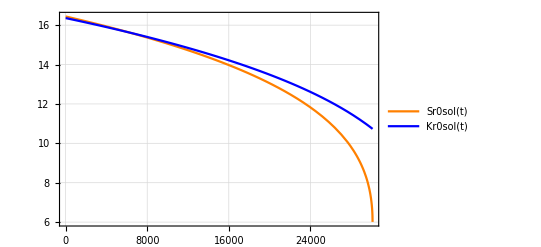

```mathematica
Plot[{Sr0sol[t],Kr0sol[t]},{t,tmin,Stmax},PlotTheme->"Detailed",ImageSize->400,PlotStyle->{Orange,Blue}]
```

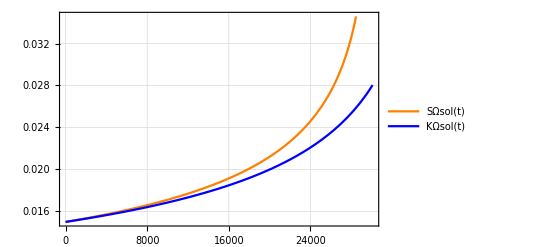

```mathematica
Plot[{SΩsol[t],KΩsol[t]},{t,tmin,Stmax},PlotTheme->"Detailed",ImageSize->400,PlotStyle->{Orange,Blue}]
```

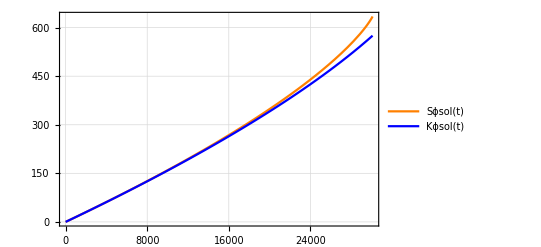

```mathematica
Plot[{Sϕsol[t],Kϕsol[t]},{t,tmin,Stmax},PlotTheme->"Detailed",ImageSize->400, PlotStyle->{Orange,Blue}]
```

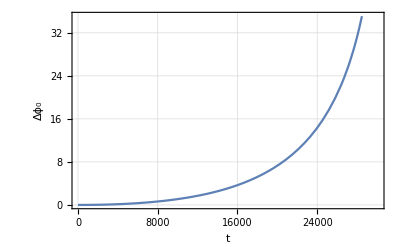

```mathematica
Plot[{Sϕsol[t]-Kϕsol[t]},{t,tmin,Stmax},PlotTheme->"Detailed",ImageSize->400, PlotLegends->"Schw and Kerr Phase difference",FrameLabel->{"t","Δϕ_0"}]
```

Now add parametric plots of the inspiral in the equatorial plane, note in our units the schwarzschild BH radius is 2M = 2, and we let the radius for the kerr case be M+(M^2-a^2)^(1/2).

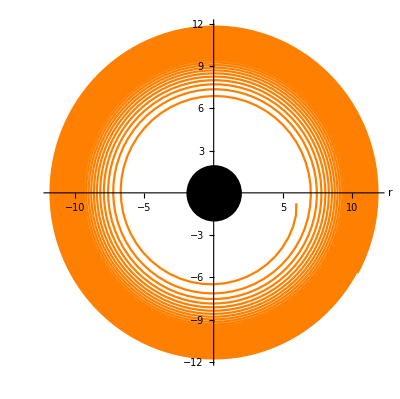

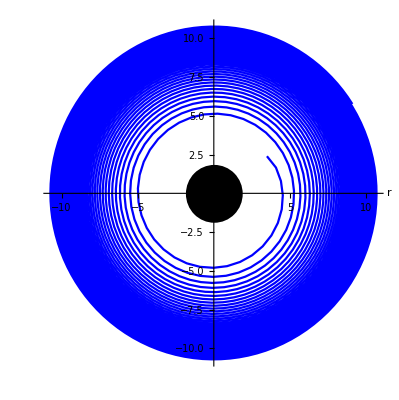

```mathematica
Show[ParametricPlot[{Sr0sol[t]Cos[Sϕsol[t]],Sr0sol[t]Sin[Sϕsol[t]]},{t,24000,Stmax}, PlotStyle->Orange, AxesLabel->{"r"}],Graphics[Disk[{0,0},2]]]
Show[ParametricPlot[{Kr0sol[t]Cos[Kϕsol[t]],Kr0sol[t]Sin[Kϕsol[t]]},{t,30000,Ktmax}, PlotStyle->Blue,AxesLabel->{"r"}],Graphics[Disk[{0,0},M+(M^2-Ka^2)^(1/2)]]]
```

### Construct and plot the waveform

We construct our waveform by first multiplying the amplitude by the phase

```mathematica
Sh[t_]:=ν ShAmp[Sr0sol[t]] ⅇ^(-ⅈ (m Sϕsol[t]+Arg[ShAmp[Sr0sol[0]]]));
Kh[t_]:=ν KhAmp[Kr0sol[t]] ⅇ^(-ⅈ (m Kϕsol[t]+Arg[KhAmp[Kr0sol[0]]]));
```

Plot our kerr and schwarzschild waveforms

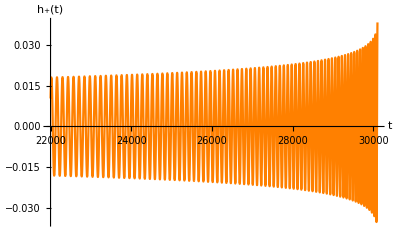

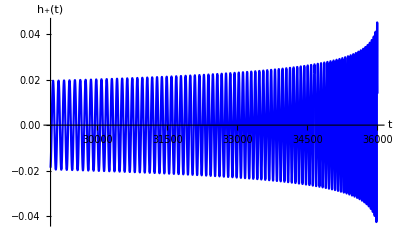

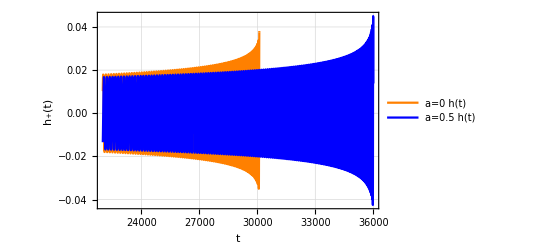

```mathematica
Show[Plot[Re[Sh[t]],{t,22000,Stmax},PlotPoints->1000, PlotStyle->Orange, AxesLabel->{"t","h_+(t)"}],PlotRange->All]
Show[Plot[Re[Kh[t]],{t,29000,Ktmax},PlotPoints->1000,PlotStyle->Blue,AxesLabel->{"t","h_+(t)"}],PlotRange->All]
Plot[{Piecewise[{{Re[Sh[t]],t<Stmax}},Indeterminate],Re[Kh[t]]},{t,22000,Ktmax},PlotPoints->1000,PlotTheme->"Detailed",ImageSize->400, PlotRange->All, PlotLegends->{"a=0 h(t)","a=0.5 h(t)"}, PlotStyle->{Orange,Blue},AxesLabel->{"t","h_+(t)"},FrameLabel->{"t","h_+(t)"}]
```

## Comparing prograde and retrograde Kerr waveforms

### Solving the ODEs

Note we denote any parameters or functions etc. with the letter P or R, corresponding to the prograde or retrograde cases respectively. Set our values for the BH spin.

```mathematica
Pa = 0.5`64;   (* prograde *)
Ra=-0.5`64;   (* retrograde *)
Pr0init = M^(1/3)(1/Ωinit - Pa)^(2/3)
Rr0init = M^(1/3)(1/Ωinit - Ra)^(2/3)
```

16.3591

16.5235

In order to reduce calculations, we interpolate a list of flux values, consisting of the sum of the infinity and horizon fluxes, summed over a wide range of l and m modes (note that the mode sum is a converging one, so we stop after l = 10). This is done for values of the radius from 4.2 (prograde) or 7.5 (retrograde) to 20, in increments of 0.1

4.233

7.55458

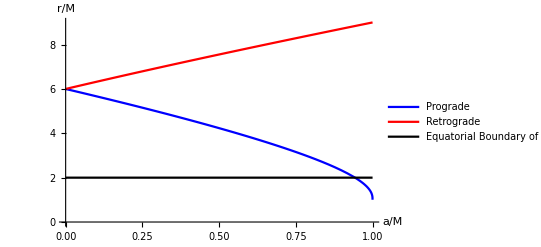

```mathematica
Pℱ=Interpolation[ ,InterpolationOrder->8];
Rℱ=Interpolation[,InterpolationOrder->8];
PhAmp=Interpolation[,InterpolationOrder->8];
RhAmp=Interpolation[,InterpolationOrder->8];
KerrGeoSeparatrix[0.5,0,1]
KerrGeoSeparatrix[0.5,0,-1]
Plot[{KerrGeoSeparatrix[x,0,1],KerrGeoSeparatrix[x,0,-1], 2},{x,0,1}, PlotLegends->{"Prograde","Retrograde", "Equatorial Boundary of Ergosphere"}, PlotStyle->{Blue,Red, Black},AxesLabel->{"a/M","r/M"}]
```

```mathematica
{PΩsol,Pϕsol,Pr0sol}=NDSolveValue[{
PΩ0'[t]==(3 Pr0[t]^3 (-3 M+2 Pa √(M/Pr0[t])+Pr0[t])^(3/2)ν Pℱ[Pr0[t]])/(√M (Pa √M+Pr0[t]^(3/2))^2 (-3 Pa^2+8 Pa √(M Pr0[t])+Pr0[t] (-6 M+Pr0[t]))),
Pϕ0'[t]==PΩ0[t],
PΩ0[t]== (Pa+(Pr0[t]/M^(1/3))^(3/2))^-1,
Pr0[0]==Pr0init,
Pϕ0[0]==ϕinit,
WhenEvent[Pr0[t]≤ 4.234, "StopIntegration"]},{PΩ0,Pϕ0,Pr0},{t,0,∞},PrecisionGoal->10,AccuracyGoal->10];
{tmin,Ptmax}=Pr0sol["Domain"][[1]];
{RΩsol,Rϕsol,Rr0sol}=NDSolveValue[{
RΩ0'[t]==(3 Rr0[t]^3 (-3 M+2 Ra √(M/Rr0[t])+Rr0[t])^(3/2)ν Rℱ[Rr0[t]])/(√M (Ra √M+Rr0[t]^(3/2))^2 (-3 Ra^2+8 Ra √(M Rr0[t])+Rr0[t] (-6 M+Rr0[t]))),
Rϕ0'[t]==RΩ0[t],
RΩ0[t]== (Ra+(Rr0[t]/M^(1/3))^(3/2))^-1,
Rr0[0]==Rr0init,
Rϕ0[0]==ϕinit,
WhenEvent[Rr0[t]≤ 7.555, "StopIntegration"]},{RΩ0,Rϕ0,Rr0},{t,0,∞},PrecisionGoal->10,AccuracyGoal->10];
{tmin,Rtmax}=Rr0sol["Domain"][[1]];
Ptmax
Rtmax
```

36000.7

18857.5

Now we plot the solutions of these equations to see how they evolve in time.

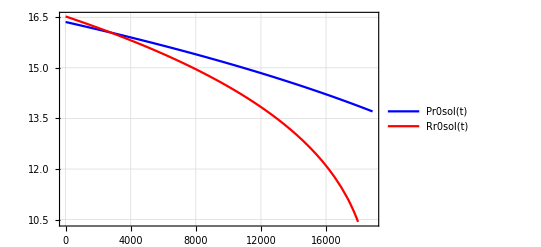

```mathematica
Plot[{Pr0sol[t],Rr0sol[t]},{t,tmin,Rtmax},PlotTheme->"Detailed",ImageSize->400, PlotStyle->{Blue,Red}]
```

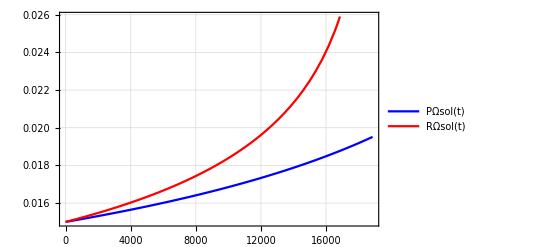

```mathematica
Plot[{PΩsol[t],RΩsol[t]},{t,tmin,Rtmax},PlotTheme->"Detailed",ImageSize->400, PlotStyle->{Blue,Red}]
```

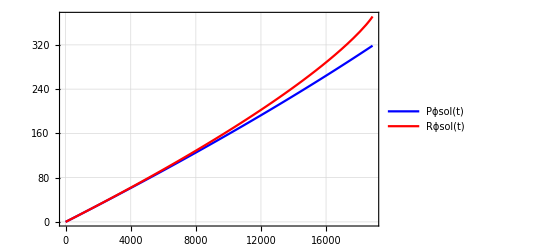

```mathematica
Plot[{Pϕsol[t],Rϕsol[t]},{t,tmin,Rtmax},PlotTheme->"Detailed",ImageSize->400, PlotStyle->{Blue,Red}]
```

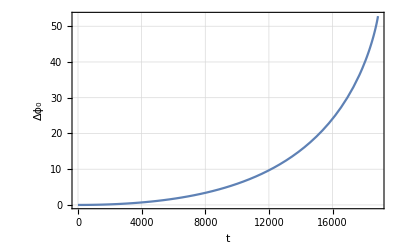

```mathematica
Plot[{Rϕsol[t]-Pϕsol[t]},{t,tmin,Rtmax},PlotTheme->"Detailed",ImageSize->400,FrameLabel->{"t","Δϕ_0"}, PlotLegends->"Prograde and Retrograde Phase difference"]
```

Now look at parametric plots of the inspiral in the equatorial plane.

-Graphics-

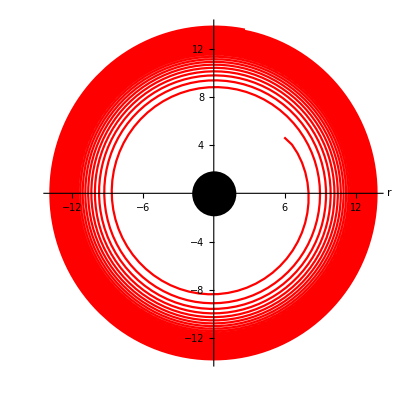

```mathematica
Show[ParametricPlot[{Pr0sol[t]Cos[Pϕsol[t]],Pr0sol[t]Sin[Pϕsol[t]]},{t,30000,Ptmax},PlotStyle->Blue,AxesLabel->{"r"}],Graphics[Disk[{0,0},M+(M^2-Pa^2)^(1/2)]]]
Show[ParametricPlot[{Rr0sol[t]Cos[Rϕsol[t]],Rr0sol[t]Sin[Rϕsol[t]]},{t,12000,Rtmax},PlotStyle->Red,AxesLabel->{"r"}],Graphics[Disk[{0,0},M+(M^2-Ra^2)^(1/2)]]]
```

### Construct and plot the waveform

We construct our waveform by first multiplying the amplitude by the phase

```mathematica
Ph[t_]:=ν PhAmp[Pr0sol[t]] ⅇ^(-ⅈ (m Pϕsol[t]+Arg[PhAmp[Pr0sol[0]]]));
Rh[t_]:=ν RhAmp[Rr0sol[t]] ⅇ^(-ⅈ (m Rϕsol[t]+Arg[RhAmp[Rr0sol[0]]]));
```

Plot our kerr and schwarzschild waveforms

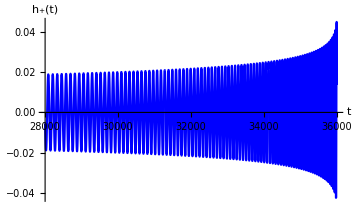

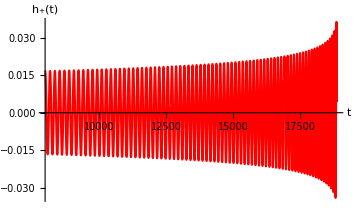

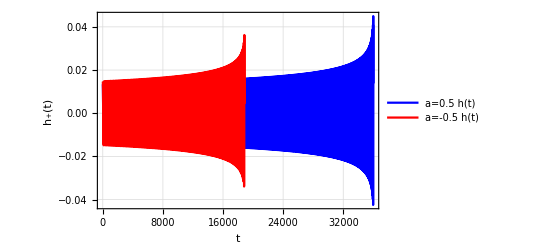

```mathematica
Show[Plot[Re[Ph[t]],{t,28000,Ptmax},PlotPoints->1000, PlotStyle->Blue,AxesLabel->{"t","h_+(t)"}],PlotRange->All]
Show[Plot[Re[Rh[t]],{t,8000,Rtmax},PlotPoints->1000,PlotStyle->Red,AxesLabel->{"t","h_+(t)"}],PlotRange->All]
Plot[{Re[Ph[t]],Piecewise[{{Re[Rh[t]],t<Rtmax}},Indeterminate]},{t,tmin,Ptmax},PlotPoints->1000,PlotTheme->"Detailed",ImageSize->400, PlotRange->All,PlotLegends->{"a=0.5 h(t)","a=-0.5 h(t)"}, PlotStyle->{Blue,Red},FrameLabel->{"t","h_+(t)"}]
```

## Comparing different spins for (prograde) Kerr waveforms

### Solving the ODEs

Note we denote any parameters or functions etc. with the number FK, SK or NK, corresponding to the kerr case with spin a = 0.5, 0.7, 0.9  respectively. Set our values for the BH spin and initial separation.

```mathematica
FKa=0.5`64;
SKa =0.7`64;
NKa=0.9`64;  
FKr0init = M^(1/3)(1/Ωinit - FKa)^(2/3)
SKr0init = M^(1/3)(1/Ωinit - SKa)^(2/3)
NKr0init = M^(1/3)(1/Ωinit - NKa)^(2/3)
```

16.3591

16.3261

16.2931

In order to reduce calculations, we interpolate a list of flux values, consisting of the sum of the infinity and horizon fluxes, summed over a wide range of l and m modes (note that the mode sum is a converging one, so we stop after l = 10). This is done for values of the radius from 4.2 to 30 for the kerr case, and 6 to 30 for the schwarzschild case, in increments of 0.1

```mathematica
FKℱ=Interpolation[ ,InterpolationOrder->8];
SKℱ=Interpolation[ ,InterpolationOrder->8];
NKℱ=Interpolation[,InterpolationOrder->8];
FKhAmp=Interpolation[,InterpolationOrder->8];
SKhAmp=Interpolation[,InterpolationOrder->8];
NKhAmp=Interpolation[,InterpolationOrder->8];
```

```mathematica
{FKΩsol,FKϕsol,FKr0sol}=NDSolveValue[{
FKΩ0'[t]==(3 FKr0[t]^3 (-3 M+2 FKa √(M/FKr0[t])+FKr0[t])^(3/2)ν FKℱ[FKr0[t]])/(√M (FKa √M+FKr0[t]^(3/2))^2 (-3 FKa^2+8 FKa √(M FKr0[t])+FKr0[t] (-6 M+FKr0[t]))),
FKϕ0'[t]==FKΩ0[t],
FKΩ0[t]== (FKa+(FKr0[t]/M^(1/3))^(3/2))^-1,
FKr0[0]==FKr0init,
FKϕ0[0]==ϕinit,
WhenEvent[FKr0[t]≤ 4.234, "StopIntegration"]},{FKΩ0,FKϕ0,FKr0},{t,0,∞},PrecisionGoal->10,AccuracyGoal->10];
{tmin,FKtmax}=FKr0sol["Domain"][[1]];
{SKΩsol,SKϕsol,SKr0sol}=NDSolveValue[{
SKΩ0'[t]==(3 SKr0[t]^3 (-3 M+2 SKa √(M/SKr0[t])+SKr0[t])^(3/2)ν SKℱ[SKr0[t]])/(√M (SKa √M+SKr0[t]^(3/2))^2 (-3 SKa^2+8 SKa √(M SKr0[t])+SKr0[t] (-6 M+SKr0[t]))),
SKϕ0'[t]==SKΩ0[t],
SKΩ0[t]== (SKa+(SKr0[t]/M^(1/3))^(3/2))^-1,
SKr0[0]==SKr0init,
SKϕ0[0]==ϕinit,
WhenEvent[SKr0[t]≤ 4.234, "StopIntegration"]},{SKΩ0,SKϕ0,SKr0},{t,0,∞},PrecisionGoal->10,AccuracyGoal->10];
{tmin,SKtmax}=SKr0sol["Domain"][[1]];
{NKΩsol,NKϕsol,NKr0sol}=NDSolveValue[{
NKΩ0'[t]==(3 NKr0[t]^3 (-3 M+2 NKa √(M/NKr0[t])+NKr0[t])^(3/2)ν NKℱ[NKr0[t]])/(√M (NKa √M+NKr0[t]^(3/2))^2 (-3 NKa^2+8 NKa √(M NKr0[t])+NKr0[t] (-6 M+NKr0[t]))),
NKϕ0'[t]==NKΩ0[t],
NKΩ0[t]== (NKa+(NKr0[t]/M^(1/3))^(3/2))^-1,
NKr0[0]==NKr0init,
NKϕ0[0]==ϕinit,
WhenEvent[NKr0[t]≤ 4.234, "StopIntegration"]},{NKΩ0,NKϕ0,NKr0},{t,0,∞},PrecisionGoal->10,AccuracyGoal->10];
{tmin,NKtmax}=NKr0sol["Domain"][[1]];
FKtmax
SKtmax
NKtmax
```

36000.7

38297.5

40479.6

Now we plot the solutions of these equations to see how they evolve in time.

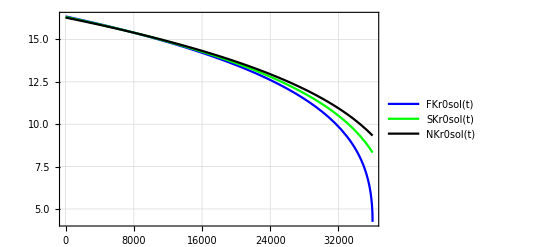

```mathematica
Plot[{FKr0sol[t],SKr0sol[t], NKr0sol[t]},{t,tmin,FKtmax},PlotTheme->"Detailed",ImageSize->400, PlotStyle->{Blue,Green, Black}]
```

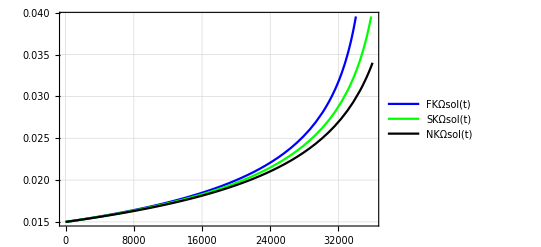

```mathematica
Plot[{FKΩsol[t],SKΩsol[t],NKΩsol[t]},{t,tmin,FKtmax},PlotTheme->"Detailed",ImageSize->400,PlotStyle->{Blue,Green,Black}]
```

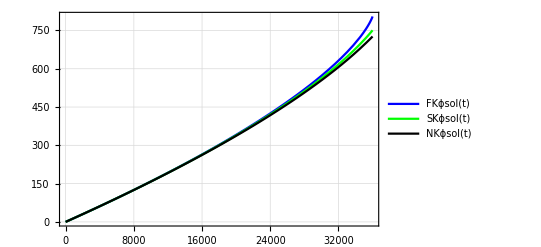

```mathematica
Plot[{FKϕsol[t],SKϕsol[t],NKϕsol[t]},{t,tmin,FKtmax},PlotTheme->"Detailed",ImageSize->400, PlotStyle->{Blue,Green,Black}]
```

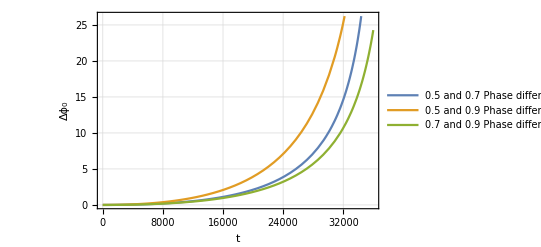

```mathematica
Plot[{FKϕsol[t]-SKϕsol[t], FKϕsol[t]-NKϕsol[t], SKϕsol[t]-NKϕsol[t]},{t,tmin,FKtmax},PlotTheme->"Detailed",ImageSize->400, PlotLegends->{"0.5 and 0.7 Phase difference", "0.5 and 0.9 Phase difference", "0.7 and 0.9 Phase difference"},FrameLabel->{"t","Δϕ_0"}]
```

Now look at parametric plots for the inspiral in the equatorial plane.

-Graphics-

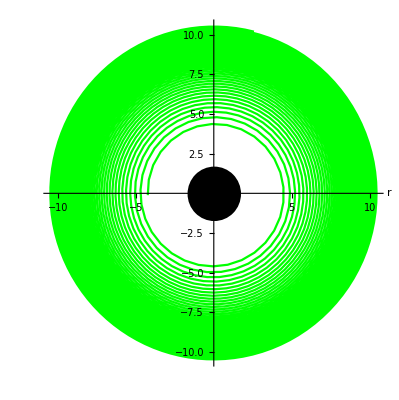

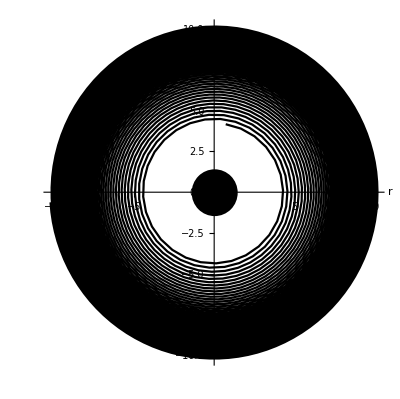

```mathematica
Show[ParametricPlot[{FKr0sol[t]Cos[FKϕsol[t]],FKr0sol[t]Sin[FKϕsol[t]]},{t,30000,FKtmax},PlotStyle->Blue,AxesLabel->{"r"}],Graphics[Disk[{0,0},M+(M^2-FKa^2)^(1/2)]]]
Show[ParametricPlot[{SKr0sol[t]Cos[SKϕsol[t]],SKr0sol[t]Sin[SKϕsol[t]]},{t,32000,SKtmax},PlotStyle->Green,AxesLabel->{"r"}],Graphics[Disk[{0,0},M+(M^2-SKa^2)^(1/2)]]]
Show[ParametricPlot[{NKr0sol[t]Cos[NKϕsol[t]],NKr0sol[t]Sin[NKϕsol[t]]},{t,34000,NKtmax},PlotStyle->Black,AxesLabel->{"r"}],Graphics[Disk[{0,0},M+(M^2-NKa^2)^(1/2)]]]
```

### Construct and plot the waveform

We construct our waveform by first multiplying the amplitude by the phase

```mathematica
FKh[t_]:=ν FKhAmp[FKr0sol[t]] ⅇ^(-ⅈ (m FKϕsol[t]+Arg[FKhAmp[FKr0sol[0]]]));
SKh[t_]:=ν SKhAmp[SKr0sol[t]] ⅇ^(-ⅈ (m SKϕsol[t]+Arg[SKhAmp[SKr0sol[0]]]));
NKh[t_]:=ν NKhAmp[NKr0sol[t]] ⅇ^(-ⅈ (m NKϕsol[t]+Arg[NKhAmp[NKr0sol[0]]]));
```

Plot our kerr and schwarzschild waveforms

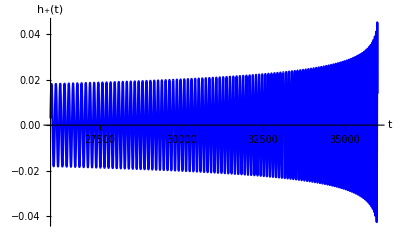

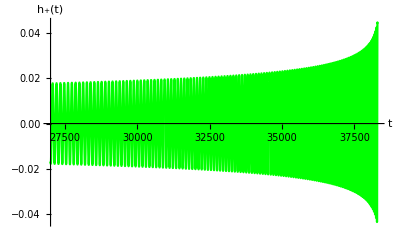

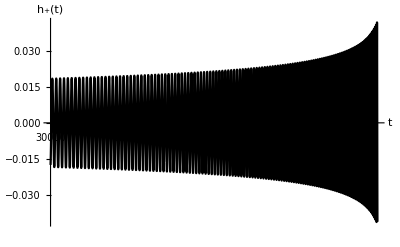

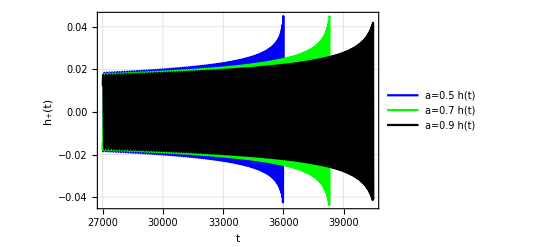

```mathematica
Show[Plot[Re[FKh[t]],{t,26000,FKtmax},PlotPoints->1000 ,PlotStyle->Blue,AxesLabel->{"t","h_+(t)"}],PlotRange->All]
Show[Plot[Re[SKh[t]],{t,27000,SKtmax},PlotPoints->1000,PlotStyle->Green,AxesLabel->{"t","h_+(t)"}],PlotRange->All]
Show[Plot[Re[NKh[t]],{t,30000,NKtmax}, PlotPoints->1000,PlotStyle->Black,AxesLabel->{"t","h_+(t)"}],PlotRange->All]
Plot[{Piecewise[{{Re[FKh[t]],t<FKtmax}},Indeterminate],Piecewise[{{Re[SKh[t]],t<SKtmax}},Indeterminate],Re[NKh[t]]},{t,27000,NKtmax},PlotPoints->1000,PlotTheme->"Detailed",ImageSize->400, PlotRange->All,PlotLegends->{"a=0.5 h(t)","a=0.7 h(t)","a=0.9 h(t)"},PlotStyle->{Blue,Green,Black},FrameLabel->{"t","h_+(t)"}]
```